```mathematica
thetaInit =(Pi/2-0.01);
Integrate[1/(Sin[x]-Sin[thetaInit])^(1/2), {x, thetaInit, Pi/2}]
```

2.22145

```mathematica
Pi/(2)^(1/2)
```

π/(√2)

```mathematica
N[π/(√2),9]
```

2.22144147

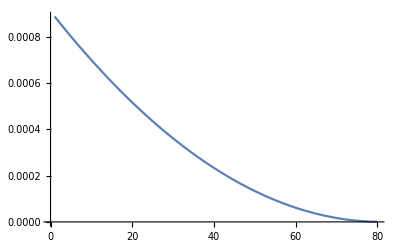

```mathematica
ClearAll[n]
n= { };
For[i = 0, i<80, i++, AppendTo[n,Re[Integrate[1/(Sin[x]-Sin[(Pi/2-0.001*(80-i))])^(1/2), {x, (Pi/2-0.01*(80-i)), Pi/2}]]-(Pi/(2)^(1/2))];]
ListLinePlot[n]
```